```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
SetOptions[Plot,BaseStyle->{FontSize->14}];
SetOptions[Graphics,BaseStyle->{FontSize->14}];
SetOptions[ParametricPlot,BaseStyle->{FontSize->14}];
SetOptions[LogPlot,BaseStyle->{FontSize->14}];
```

```mathematica
ZO=2T Sqrt[1+R/(2x)];
ZI=2Sqrt[2*Rp*(x+T/2)]
```

2 √2 √(Rp (T/2+x))

```mathematica
Solve[(ZO/.x->(T/2))==(ZI/.x->(T/2)),Rp]
```

{{Rp→(R+T)/2}}

```mathematica
ZI=ZI/.Solve[{(ZO/.x->(T/2))==(ZI/.x->(T/2))},Rp];
ZI=ZI[[1]]
```

2 √((R+T) (T/2+x))

```mathematica
Z1=ZI*If[-T/2≤x≤T/2,1,0]+ZO*If[T/2<x,1,0]
```

2 T √(1+R/(2 x)) If[T/2<x,1,0]+2 √((R+T) (T/2+x)) If[-T/2≤x≤T/2,1,0]

```mathematica
mas=4.84814*^-9;
AU=1.495978707*^11;
c=2.99792458*^8;
pc=3.0857*^16;
re=2.8179403227*^-15;
dlens=389.*pc;
dpsr=620.*pc;

λ=c/314.5*^6;
λA=1.*^5*AU;
T=0.01*AU;
A=0.3*AU;
inc=1.*^-5;

R=λA^2/(4π^2A Cos[inc]^3 Sqrt[1.-λA^2./(4.π^2 A^2)Tan[inc]^2]);
s=1.-dlens/dpsr;
r=R/dlens;
t=T/dlens; 
R/pc
T/AU
r
t/mas

Δn:=-λ^2/(2π)Δne re
Δnes={0.003,0.03,0.3,3.}*1.*^6;
```

4829.05

0.01

12.414

0.0257067

```mathematica
Z=Convolve[Z1,PDF[NormalDistribution[0,T/2],x],x,y]
```

5.33353×10^-10 ((2.15253×10^24+0. ⅈ) ⅇ^(-1.33692×10^-9 y)+2.99196×10^9 Convolve[√(1+(7.4505×10^19)/x) If[7.47989×10^8<x,1,0],ⅇ^(-8.93674×10^-19 x^2),x,y])

```mathematica
alphahat=-Δn Re[D[Z,y]]
```

4.07523×10^-16 Δne (0.+5.33353×10^-10 Re[(-2.87776×10^15+0. ⅈ) ⅇ^(-1.33692×10^-9 y)+2.99196×10^9 (0.+Convolve^(0,0,0,1)[√(1+(7.4505×10^19)/x) If[7.47989×10^8<x,1,0],ⅇ^(-8.93674×10^-19 x^2),x,y]+(0.+√(1+(7.4505×10^19)/x) If[7.47989×10^8<x,0,0]) Convolve^(1,0,0,0)[√(1+(7.4505×10^19)/x) If[7.47989×10^8<x,1,0],ⅇ^(-8.93674×10^-19 x^2),x,y])])

```mathematica
β:=θ-s*alphahat
```

```mathematica
μ:=1./D[β,θ]
```

```mathematica
β/.Δne->Δnes[[3]]/.y->θ*dlens/.θ->10.*mas
```

4.84814×10^-8-4.55505×10^-11 (0.+5.33353×10^-10 (-3.76071804855547×10^-323+2.99196×10^9 (0.+Re[Convolve^(0,0,0,1)[√(1+(7.4505×10^19)/x) If[7.47989×10^8<x,1,0],ⅇ^(-8.93674×10^-19 x^2),x,5.8194×10^11]+(0.+√(1+(7.4505×10^19)/x) If[7.47989×10^8<x,0,0]) Convolve^(1,0,0,0)[√(1+(7.4505×10^19)/x) If[7.47989×10^8<x,1,0],ⅇ^(-8.93674×10^-19 x^2),x,5.8194×10^11]])))

```mathematica
ParametricPlot[{β/mas/.Δne->Δnes[[3]],θ/mas},{θ,-100*mas,100*mas},PlotStyle->{Directive[Red]}
,PlotRange->{{-100,100},{-1,1}},AxesLabel->{"β [mas]","θ [mas]"},ImageSize->400,ImagePadding->{{0,60},{0,60}},AspectRatio->1]
```

-Graphics-

```mathematica
ParametricPlot[{β/mas/.Δne->Δnes[[3]],θ/mas},{θ,-20*mas,20*mas},PlotStyle->{Directive[Red]}
,PlotRange->{{-20,20},{-0.01,0.01}},AxesLabel->{"β [mas]","θ [mas]"},ImageSize->400,ImagePadding->{{0,60},{0,60}},AspectRatio->1]
```

-Graphics-

```mathematica
ts=Solve[{beta==β},θ,Reals]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{beta==θ-61046.3 ⅇ^(-6.43807×10^19 θ^2) Δne θ √Abs[θ] (BesselI[-5/4,6.43807×10^19 θ^2]-2 BesselI[-1/4,6.43807×10^19 θ^2]+BesselI[3/4,6.43807×10^19 θ^2]+(BesselI[-3/4,6.43807×10^19 θ^2]-2 BesselI[1/4,6.43807×10^19 θ^2]+BesselI[5/4,6.43807×10^19 θ^2]) If[θ≥0,1,-1])},θ,Reals]

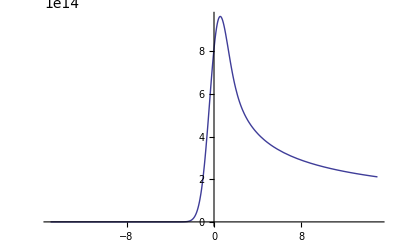

```mathematica
Plot[Re[Z],{y,-10.*T,10.*T},PlotRange->All]
```

```mathematica
Plot[D[Re[Z],y],{y,-10*T,10*T}]
```

General::ivar: -1.49592×10^10 is not a valid variable.

General::ivar: -1.43486×10^10 is not a valid variable.

General::ivar: -1.3738×10^10 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-